```mathematica
NN = 1000
```

1000

```mathematica
f1[μ_,θ_] := Exp[1/NN Log[( 1 + (-1)^NN μ^NN ⅇ^(ⅈ NN θ) )]]
```

```mathematica
f[μ_,θ_] :=  ⅇ^(- ⅈ θ) Exp[1/NN Log[( 1 + (-1)^NN μ^NN ⅇ^(ⅈ NN θ) )]]
```

```mathematica
θ = π/10
```

π/10

```mathematica
FindRoot[ { Re [ f[μ,0.7] ] == 0 }, { μ, 2.0} ]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {μ} = {1.9083092883676045`*^-9}. Try perturbing the initial point(s).

{μ→1.90831×10^-9}

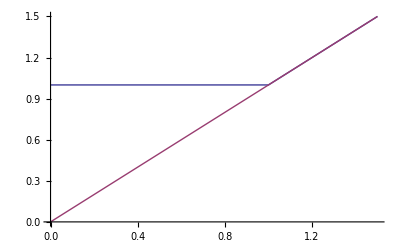

```mathematica
Plot[{ Abs[f1[μ, 0.7]], μ}, { μ, 0., 1.5 }]
```

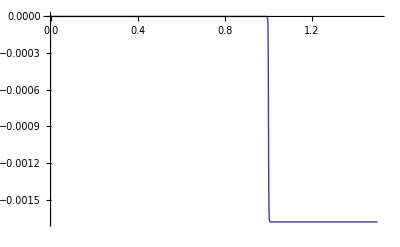

```mathematica
Plot[{ Arg[f1[μ, 1.5]] } ,  { μ, 0., 1.5 } ]
```

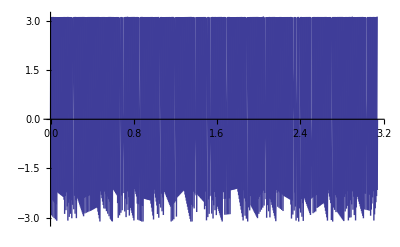

```mathematica
Plot[{Arg[f1[1.5, θ]] * 1000}, { θ, 0., π }]
```

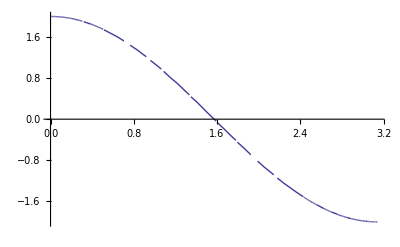

```mathematica
Plot[ Re[f[2.0, θ]], {θ, 0., π} ]
```

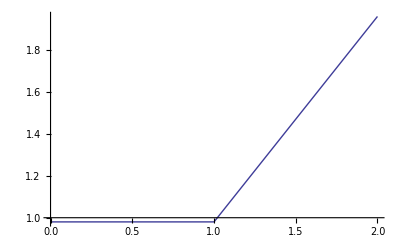

```mathematica
Plot[{Re[f[μ, 0.2]]}, {μ, 0.,2.}]
```

```mathematica
f[2.0, θ] // N
```

1.90211-0.618034 ⅈ